```mathematica
Clear["Global`*"]
dir=NotebookDirectory[];
m=0.086;
g=9.81;
J=1/12 m(0.02^2+0.035^2);
L=0.035;
(*u1max=1.224;
u2max=0.08925L;*)
Fmax=0.612;
scale=4050;
K1=7;

(*Change between original and new controller*)
D1=1.42;
K2=1.5;(*Original:1.5, New:7*)
D2=1.95;(*Original:1.95, New:3*)
(*Change between original and new controller*)

K3=.04;
D3=.002;
ωmax=19200/60*2π;
ωmin=10000/60*2π;
xp[t_]:=0
yp[t_]:=0
u11=m g+K1 (y[t]-yp[t])+D1( y'[t]-D[yp[t],t]);
(*ϕdes=Sign[K2 x[t]+D2 x'[t]]*Min[Abs[K2 x[t]+D2 x'[t]],0.2];*)
ϕdes=0.2Tanh[K2 (x[t]-xp[t])+D2 (x'[t]-D[xp[t],t])];
u21=K3(ϕdes-ϕ[t])+D3 (-ϕ'[t]);
(*Eredeti: u21=K3(ϕdes-ϕ[t])+D3 (D[ϕdes,t]-ϕ'[t]);*)
ω11=(u11+2 u21/L)/2 scale;
ω21=(u11-2 u21/L)/2 scale;
ω1=Max[Min[ω11,ωmax],ωmin];
ω2=Max[Min[ω21,ωmax],ωmin];
F1=lift[ω1,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]-L*ϕ'[t]];
F2=lift[ω2,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]+L*ϕ'[t]];
u1=F1+F2;
u2=L/2(F1-F2);
eqs={x''[t]==(u1 Sin[ϕ[t]])/m,y''[t]==-g+(u1 Cos[ϕ[t]])/m,ϕ''[t]==u2/J};
```

```mathematica
(*Simulate the system with both lift models. The params for the lift model are in order: ω,vx,vy*)
liftnew[ω_,vx_,vy_]:=-2*(0.0005917217101953038 vx^2-0.00002557102446913359 vx^4-0.0009764562665337519 vy-0.00013859859899200091 vx^2 vy+0.00004560884655456854 vy^3-7.893807214858706*^-8 ω^2);
liftorig[ω_,vx_,vy_]:=1.5042947579635582*^-7 ω^2;
Simulate[xpa_,ypa_,T_,IC_:{1,0,0,0,0,0},eqss_]:=<|
"orig"->NDSolve[(eqss/.{xp->xpa,yp->ypa,lift->liftorig})&&x[0]==IC[[1]]&&y[0]==IC[[2]]&&ϕ[0]==IC[[3]]&&x'[0]==IC[[4]]&&y'[0]==IC[[5]]&&ϕ'[0]==IC[[6]],{x[t],y[t],ϕ[t]},{t,0,T}][[1]],"new"->NDSolve[(eqss/.{xp->xpa,yp->ypa,lift->liftnew})&&x[0]==IC[[1]]&&y[0]==IC[[2]]&&ϕ[0]==IC[[3]]&&x'[0]==IC[[4]]&&y'[0]==IC[[5]]&&ϕ'[0]==IC[[6]],{x[t],y[t],ϕ[t]},{t,0,T}][[1]]|>
(*Plot omegas*)
ComputeEqs[K1_,D1_,K2_,D2_,K3_,D3_]:=(
u11=m g-K1 (y[t]-yp[t])-D1( y'[t]-D[yp[t],t]);
(*ϕdes=Sign[K2 x[t]+D2 x'[t]]*Min[Abs[K2 x[t]+D2 x'[t]],0.2];*)
ϕdes=0.12Tanh[-K2 (x[t]-xp[t])-D2 (x'[t]-D[xp[t],t])];
u21=K3(ϕdes-ϕ[t])+D3 (-ϕ'[t]);
(*Eredeti: u21=K3(ϕdes-ϕ[t])+D3 (D[ϕdes,t]-ϕ'[t]);*)
ω1=(u11+2 u21/L)/2 scale;
ω2=(u11-2 u21/L)/2 scale;
F1=lift[ω1,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]-L*ϕ'[t]];
F2=lift[ω2,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]+L*ϕ'[t]];
u1=F1+F2;
u2=L/2(F1-F2);

Return[{x''[t]==(u1 Sin[ϕ[t]])/m,y''[t]==-g+(u1 Cos[ϕ[t]])/m,ϕ''[t]==u2/J}])
ComputeEqsSaturation[K1_,D1_,K2_,D2_,K3_,D3_]:=(
u11=m g-K1 (y[t]-yp[t])-D1( y'[t]-D[yp[t],t]);
(*ϕdes=Sign[K2 x[t]+D2 x'[t]]*Min[Abs[K2 x[t]+D2 x'[t]],0.2];*)
ϕdes=0.12Tanh[-K2 (x[t]-xp[t])-D2 (x'[t]-D[xp[t],t])];
u21=K3(ϕdes-ϕ[t])+D3 (-ϕ'[t]);
(*Eredeti: u21=K3(ϕdes-ϕ[t])+D3 (D[ϕdes,t]-ϕ'[t]);*)
ω1=Max[Min[(u11+2 u21/L)/2 scale,ωmax],ωmin];
ω2=Max[Min[(u11-2 u21/L)/2 scale,ωmax],ωmin];
F1=lift[ω1,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]-L*ϕ'[t]];
F2=lift[ω2,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]+L*ϕ'[t]];
u1=F1+F2;
u2=L/2(F1-F2);

Return[{x''[t]==(u1 Sin[ϕ[t]])/m,y''[t]==-g+(u1 Cos[ϕ[t]])/m,ϕ''[t]==u2/J}])
PlotOmega[sol_,ranges_,onlyoneplot_:False,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008]},{Red,Dashed,Thickness[.008]},{Orange,Dashed,Thickness[.008]}}]:=(ω1v=ω1/.Flatten[{sol[["new"]],D[sol[["new"]],t],D[D[sol[["new"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω1vorig=ω1/.Flatten[{sol[["orig"]],D[sol[["orig"]],t],D[D[sol[["orig"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω2v=ω2/.Flatten[{sol[["new"]],D[sol[["new"]],t],D[D[sol[["new"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω2vorig=ω2/.Flatten[{sol[["orig"]],D[sol[["orig"]],t],D[D[sol[["orig"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ωplot1=Plot[{ω1v,ω1vorig,ω2v,ω2vorig},{t,ranges[[1,1]],ranges[[1,2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle,Exclusions->None];
ωplot2=Plot[{ω1v,ω1vorig,ω2v,ω2vorig},{t,ranges[[2,1]],ranges[[2,2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle,Exclusions->None];
Legended[Grid[If[!onlyoneplot,{{ωplot1,ωplot2}},{{ωplot1}}]],Placed[LineLegend[Directive@@@plotstyle,{"ω_1 Data-driven model","ω_1 Base model","ω_2 Data-driven model","ω_2 Base model"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plotxy[sol_,range_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(xplot=Plot[{x[t]/.sol[["new"]],x[t]/.sol[["orig"]],xp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
yplot=Plot[{y[t]/.sol[["new"]],y[t]/.sol[["orig"]],yp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
Legended[Grid[{{xplot,yplot}}],Placed[LineLegend[Directive@@@plotstyle,{"Data-driven model","Base model","Prescribed"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plotxyϕ[sol_,range_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(xplot=Plot[{x[t]/.sol[["new"]],x[t]/.sol[["orig"]],xp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
yplot=Plot[{y[t]/.sol[["new"]],y[t]/.sol[["orig"]],yp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
ϕplot=Plot[{ϕ[t]/.sol[["new"]],ϕ[t]/.sol[["orig"]]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ϕ [rad]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
Legended[Grid[{{xplot,yplot},{ϕplot}}],Placed[LineLegend[Directive@@@plotstyle,{"Data-driven model","Base model","Prescribed"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
PlotxyϕCompare[sol1_,sol2_,range_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(xplot=Plot[{x[t]/.sol1[["new"]],x[t]/.sol2[["new"]],xp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
yplot=Plot[{y[t]/.sol1[["new"]],y[t]/.sol2[["new"]],yp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
ϕplot=Plot[{ϕ[t]/.sol1[["new"]],ϕ[t]/.sol2[["new"]]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ϕ [rad]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
Legended[Grid[{{xplot,yplot},{ϕplot}}],Placed[LineLegend[Directive@@@plotstyle,{"Data-driven model","Base model","Prescribed"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
PlotxyϕCompare3[sol1_,sol2_,sol3_,range_,plotstyle_:{{Blue,Thickness[.008]},{Orange,Thickness[.008],Dashing[{Large,Medium}]},{Green,Thickness[.008],Dashing[Large,Large]}}]:=(xplot=Plot[{x[t]/.sol1[["new"]],x[t]/.sol2[["new"]],x[t]/.sol3[["new"]]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
yplot=Plot[{y[t]/.sol1[["new"]],y[t]/.sol2[["new"]],y[t]/.sol3[["new"]]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
ϕplot=Plot[{ϕ[t]/.sol1[["new"]],ϕ[t]/.sol2[["new"]],ϕ[t]/.sol3[["new"]]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ϕ [rad]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
Legended[Grid[{{xplot,yplot},{ϕplot}}],Placed[LineLegend[Directive@@@plotstyle,{"Data-driven model controller","Base model controller","Original controller","Prescribed"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plottraj[sol_,range_,maxtimeprescribed_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(ParametricPlot[{{x[t],y[t]}/.sol[["new"]],{x[t],y[t]}/.sol[["orig"]],Piecewise[{{{xp[t],yp[t]},t<maxtimeprescribed}},Indeterminate]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{HoldForm[x" [m]"],HoldForm[y" [m]"]},LabelStyle-> {Black,FontSize->36,FontFamily->"Times"},ImageSize->Large,AspectRatio->1,PlotLegends->{"Data-driven model","Base model","Prescribed"},PlotStyle->plotstyle])
ampli[fcn_,tmin_,tmax_,dt_:10^-3]:=max[fcn,tmin,tmax,dt]-min[fcn,tmin,tmax,dt]
max[fcn_,tmin_,tmax_,dt_:10^-3]:=Max[Table[fcn,{t,tmin,tmax,dt}]]
min[fcn_,tmin_,tmax_,dt_:10^-3]:=Min[Table[fcn,{t,tmin,tmax,dt}]]
SettlingTime[fcn_,dt_,maxT_,error_]:=(tab=Table[fcn,{t,0,maxT,10^-3}];For[TT=0,TT<=maxT,TT=TT+dt,
If[Max[Drop[tab,Round[TT/10^-3]]]-Min[Drop[tab,Round[TT/10^-3]]]<error,Return[TT]]];Return[maxT])
Jacobi[K1_,D1_,K2_,D2_,K3_,D3_,lift2_]:=D[{x2,#[[1]],x4,#[[2]],x6,#[[3]]}&@ComputeEqs[K1,D1,K2,D2,K3,D3][[All,2]]/.{x[t]->x1,x'[t]->x2,y[t]->x3,y'[t]->x4,ϕ[t]->x5,ϕ'[t]->x6,lift->lift2},{{x1,x2,x3,x4,x5,x6}}]/.{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}
```

```mathematica
eqs=ComputeEqs[K1v,D1v,K2v,D2v,K3v,D3v]/.lift->liftnew
```

{x''[t]==11.6279 Sin[ϕ[t]] (-2 (0.000591722 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2-0.000025571 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^4-0.000976456 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])-0.000138599 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])+0.0000456088 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])^3-0.323695 (0.84366-K1v y[t]-D1v y'[t]-57.1429 (K3v (-0.12 Tanh[K2v x[t]+D2v x'[t]]-ϕ[t])-D3v ϕ'[t]))^2)-2 (0.000591722 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2-0.000025571 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^4-0.000976456 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])-0.000138599 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])+0.0000456088 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])^3-0.323695 (0.84366-K1v y[t]-D1v y'[t]+57.1429 (K3v (-0.12 Tanh[K2v x[t]+D2v x'[t]]-ϕ[t])-D3v ϕ'[t]))^2)),y''[t]==-9.81+11.6279 Cos[ϕ[t]] (-2 (0.000591722 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2-0.000025571 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^4-0.000976456 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])-0.000138599 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])+0.0000456088 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])^3-0.323695 (0.84366-K1v y[t]-D1v y'[t]-57.1429 (K3v (-0.12 Tanh[K2v x[t]+D2v x'[t]]-ϕ[t])-D3v ϕ'[t]))^2)-2 (0.000591722 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2-0.000025571 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^4-0.000976456 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])-0.000138599 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])+0.0000456088 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])^3-0.323695 (0.84366-K1v y[t]-D1v y'[t]+57.1429 (K3v (-0.12 Tanh[K2v x[t]+D2v x'[t]]-ϕ[t])-D3v ϕ'[t]))^2)),ϕ''[t]==1502.68 (2 (0.000591722 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2-0.000025571 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^4-0.000976456 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])-0.000138599 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])+0.0000456088 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+0.035 ϕ'[t])^3-0.323695 (0.84366-K1v y[t]-D1v y'[t]-57.1429 (K3v (-0.12 Tanh[K2v x[t]+D2v x'[t]]-ϕ[t])-D3v ϕ'[t]))^2)-2 (0.000591722 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2-0.000025571 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^4-0.000976456 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])-0.000138599 (Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t])^2 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])+0.0000456088 (-Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]-0.035 ϕ'[t])^3-0.323695 (0.84366-K1v y[t]-D1v y'[t]+57.1429 (K3v (-0.12 Tanh[K2v x[t]+D2v x'[t]]-ϕ[t])-D3v ϕ'[t]))^2))}

```mathematica
<<ToMatlab`
StringReplace[#,{" ...\n  "->"",".*"->"*",".^"->"^"}]&/@ToMatlab/@(eqs/.{ϕ[t]->phi,x'[t]->xdot,y'[t]->ydot,ϕ'[t]->phidot,x[t]->x,y[t]->y,K1v->"K1",D1v->"D1",K2v->"K2",D2v->"D2",K3v->"K3",D3v->"D3"})[[All,2]]
```

{0.116279E2*sin(phi)*((-2)*((-0.976456E-3)*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))+0.456088E-4*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))^3+0.591722E-3*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.138599E-3)*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.25571E-4)*(xdot*cos(phi)+ydot*sin(phi))^4+(-0.323695E0)*(0.84366E0+(-1)*K1*y+(-1)*D1*ydot+(-0.571429E2)*((-1)*D3*phidot+K3*((-1)*phi+(-0.12E0)*tanh(K2*x+D2*xdot))))^2)+(-2)*((-0.976456E-3)*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))+0.456088E-4*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))^3+0.591722E-3*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.138599E-3)*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.25571E-4)*(xdot*cos(phi)+ydot*sin(phi))^4+(-0.323695E0)*(0.84366E0+(-1)*K1*y+(-1)*D1*ydot+0.571429E2*((-1)*D3*phidot+K3*((-1)*phi+(-0.12E0)*tanh(K2*x+D2*xdot))))^2));
,(-0.981E1)+0.116279E2*cos(phi)*((-2)*((-0.976456E-3)*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))+0.456088E-4*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))^3+0.591722E-3*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.138599E-3)*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.25571E-4)*(xdot*cos(phi)+ydot*sin(phi))^4+(-0.323695E0)*(0.84366E0+(-1)*K1*y+(-1)*D1*ydot+(-0.571429E2)*((-1)*D3*phidot+K3*((-1)*phi+(-0.12E0)*tanh(K2*x+D2*xdot))))^2)+(-2)*((-0.976456E-3)*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))+0.456088E-4*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))^3+0.591722E-3*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.138599E-3)*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.25571E-4)*(xdot*cos(phi)+ydot*sin(phi))^4+(-0.323695E0)*(0.84366E0+(-1)*K1*y+(-1)*D1*ydot+0.571429E2*((-1)*D3*phidot+K3*((-1)*phi+(-0.12E0)*tanh(K2*x+D2*xdot))))^2));
,0.150268E4*(2*((-0.976456E-3)*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))+0.456088E-4*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))^3+0.591722E-3*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.138599E-3)*(0.35E-1*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.25571E-4)*(xdot*cos(phi)+ydot*sin(phi))^4+(-0.323695E0)*(0.84366E0+(-1)*K1*y+(-1)*D1*ydot+(-0.571429E2)*((-1)*D3*phidot+K3*((-1)*phi+(-0.12E0)*tanh(K2*x+D2*xdot))))^2)+(-2)*((-0.976456E-3)*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))+0.456088E-4*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))^3+0.591722E-3*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.138599E-3)*((-0.35E-1)*phidot+(-1)*ydot*cos(phi)+(-1)*xdot*sin(phi))*(xdot*cos(phi)+ydot*sin(phi))^2+(-0.25571E-4)*(xdot*cos(phi)+ydot*sin(phi))^4+(-0.323695E0)*(0.84366E0+(-1)*K1*y+(-1)*D1*ydot+0.571429E2*((-1)*D3*phidot+K3*((-1)*phi+(-0.12E0)*tanh(K2*x+D2*xdot))))^2));
}

## Original lift model

```mathematica
plotmin=-5.1;
plotmax=3.1;
ncont=40;
```

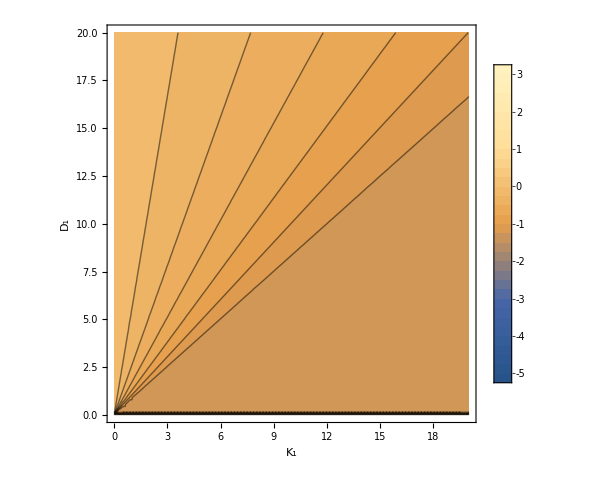

{-1.31393,{K1v→5.33041,D1v→1.17944}}

```mathematica
liftorig[ω_,vx_,vy_]:=1.5042947579635582*^-7 ω^2;
Jac1=Jacobi[K1v,D1v,K2,D2,K3,D3,liftorig];
plj1o=ContourPlot[Max[Re[Eigenvalues[Jac1]]],{K1v,0,20},{D1v,0,20},FrameLabel->{"K_1","D_1"},PlotLegends->BarLegend[{Automatic,{plotmin,plotmax}},Table[-5+0.25i,{i,0,32}]],ColorFunction->ColorData[{"M10DefaultDensityGradient",{plotmin,plotmax}}],ColorFunctionScaling->False,Contours->Table[plotmin+i*(plotmax-plotmin)/ncont,{i,0,ncont}],LabelStyle->{Black,FontFamily->Times,FontSize->26},ImageSize->500]
NMinimize[Max[Re[Eigenvalues[Jac1]]],{K1v,D1v}]
```

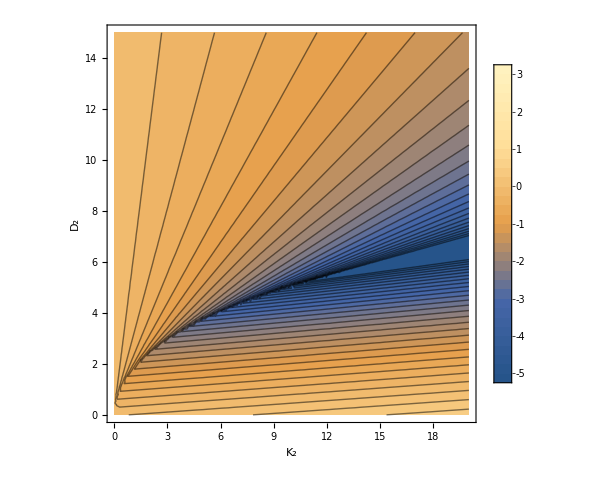

{-5.62454,{K2v→13.5584,D2v→5.72748}}

```mathematica
Jac2=Jacobi[5.33,1.18,K2v,D2v,K3,D3,liftorig];
plj2o=ContourPlot[Max[Re[Eigenvalues[Jac2]]],{K2v,0,20},{D2v,0,15},FrameLabel->{"K_2","D_2"},PlotLegends->BarLegend[{Automatic,{plotmin,plotmax}},Table[-5+0.25i,{i,0,32}]],ColorFunction->ColorData[{"M10DefaultDensityGradient",{plotmin,plotmax}}],ColorFunctionScaling->False,Contours->Table[plotmin+i*(plotmax-plotmin)/ncont,{i,0,ncont}],LabelStyle->{Black,FontFamily->Times,FontSize->26},ImageSize->500]
NMinimize[Max[Re[Eigenvalues[Jac2]]],{K2v,D2v}]
```

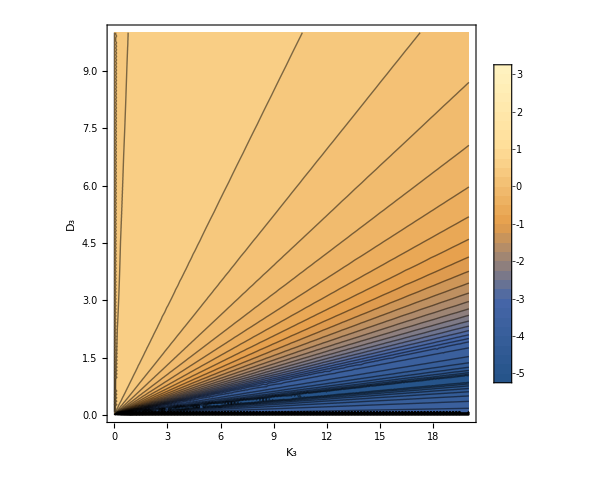

{-5.62454,{K3v→4.07275,D3v→0.200546}}

```mathematica
Jac3=Jacobi[5.33,1.18,13.56,5.73,K3v,D3v,liftorig];
plj3o=ContourPlot[Max[Re[Eigenvalues[Jac3]]],{K3v,0,20},{D3v,0,10},FrameLabel->{"K_3","D_3"},PlotLegends->BarLegend[{Automatic,{plotmin,plotmax}},Table[-5+0.25i,{i,0,32}]],ColorFunction->ColorData[{"M10DefaultDensityGradient",{plotmin,plotmax}}],ColorFunctionScaling->False,Contours->Table[plotmin+i*(plotmax-plotmin)/ncont,{i,0,ncont}],LabelStyle->{Black,FontFamily->Times,FontSize->26},ImageSize->500]
NMinimize[Max[Re[Eigenvalues[Jac3]]],{K3v,D3v}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_plj1o.png"}],plj1o]
Export[FileNameJoin[{dir,"fig/out_plj2o.png"}],plj2o]
Export[FileNameJoin[{dir,"fig/out_plj3o.png"}],plj3o]
```

D:\Users\David\Desktop\BME\Diplomamunka\Mathematica\fig\out_plj1o.png

D:\Users\David\Desktop\BME\Diplomamunka\Mathematica\fig\out_plj2o.png

D:\Users\David\Desktop\BME\Diplomamunka\Mathematica\fig\out_plj3o.png

{-35729.1+0. ⅈ,-22.9378+0. ⅈ,-7.34373+2.37054 ⅈ,-7.34373-2.37054 ⅈ,-5.68515+0. ⅈ,-5.62454+0. ⅈ}

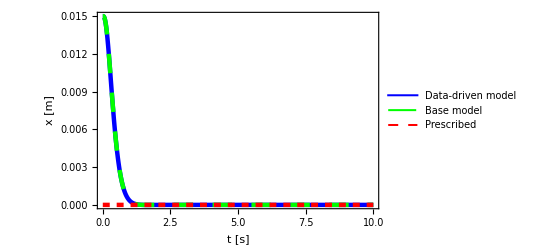
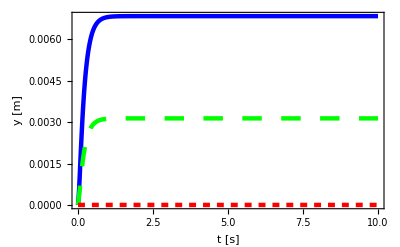
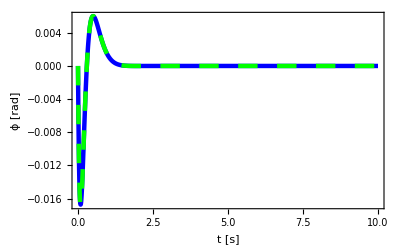
-Graphics- | -Graphics-
-Graphics- |

```mathematica
paramsorig={5.33,1.18,13.56,5.73,4.073,0.2};
Eigenvalues[Jacobi@@Flatten[{paramsorig,liftorig}]]
sol=Simulate[0,0,10,{0.015,0,0,0,0,0},ComputeEqs@@{5.33,1.18,13.56,5.73,4.073,0.2}];
Plotxyϕ[sol,{0,10}]
```

## New lift model

```mathematica
plotmin=-3.1;
plotmax=3.1;
ncont=30;
```

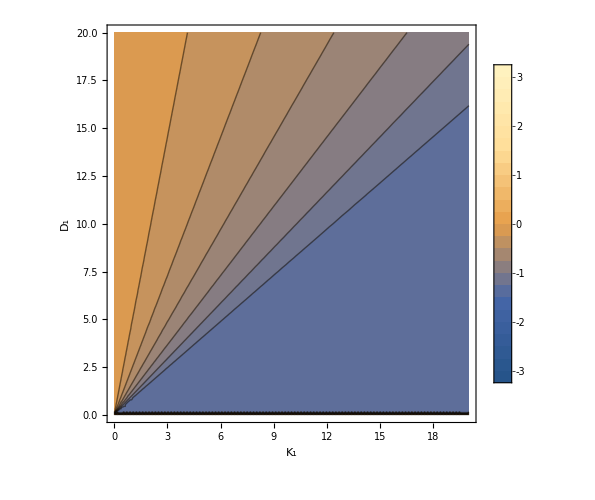

{-1.39067,{K1v→1.4184,D1v→0.514249}}

```mathematica
liftnew[ω_,vx_,vy_]:=-2*(0.0005917217101953038 vx^2-0.00002557102446913359 vx^4-0.0009764562665337519 vy-0.00013859859899200091 vx^2 vy+0.00004560884655456854 vy^3-7.893807214858706*^-8 ω^2);
Jac1=Jacobi[K1v,D1v,K2,D2,K3,D3,liftnew];
plj1d=ContourPlot[Max[Re[Eigenvalues[Jac1]]],{K1v,0,20},{D1v,0,20},FrameLabel->{"K_1","D_1"},PlotLegends->BarLegend[{Automatic,{plotmin,plotmax}},Table[-3+0.25i,{i,0,24}]],ColorFunction->ColorData[{"M10DefaultDensityGradient",{plotmin,plotmax}}],ColorFunctionScaling->False,Contours->Table[plotmin+i*(plotmax-plotmin)/ncont,{i,0,ncont}],LabelStyle->{Black,FontFamily->Times,FontSize->26},ImageSize->500]
NMinimize[Max[Re[Eigenvalues[Jac1]]],{K1v,D1v}]
```

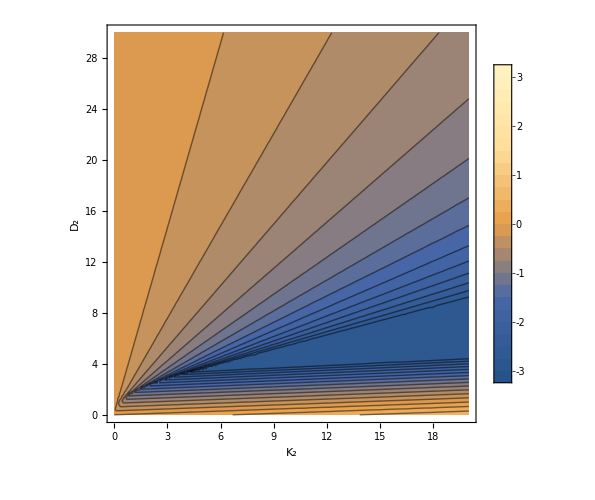

{-2.84583,{K2v→6.13181,D2v→3.99687}}

```mathematica
Jac2=Jacobi[14.2,05.1,K2v,D2v,K3,D3,liftnew];
plj2d=ContourPlot[Max[Re[Eigenvalues[Jac2]]],{K2v,0,20},{D2v,0,30},FrameLabel->{"K_2","D_2"},PlotLegends->BarLegend[{Automatic,{plotmin,plotmax}},Table[-3+0.25i,{i,0,24}]],ColorFunction->ColorData[{"M10DefaultDensityGradient",{plotmin,plotmax}}],ColorFunctionScaling->False,Contours->Table[plotmin+i*(plotmax-plotmin)/ncont,{i,0,ncont}],LabelStyle->{Black,FontFamily->Times,FontSize->26},ImageSize->500]
NMinimize[Max[Re[Eigenvalues[Jac2]]],{K2v,D2v}]
```

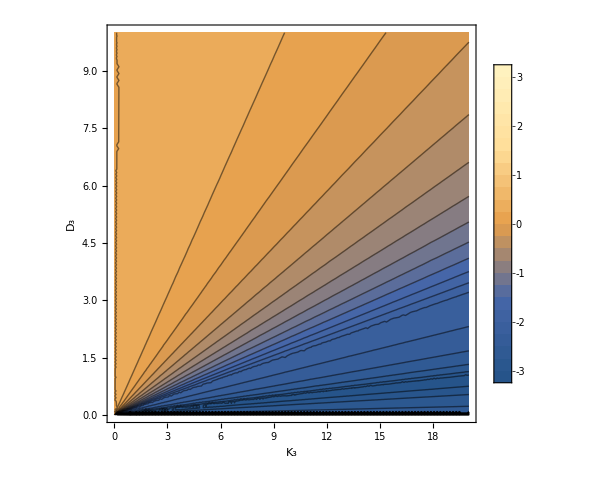

{-3.46755,{K3v→29.6976,D3v→1.47488}}

```mathematica
Jac3=Jacobi[1.42,0.51,6.13,4,K3v,D3v,liftnew];
plj3d=ContourPlot[Max[Re[Eigenvalues[Jac3]]],{K3v,0,20},{D3v,0,10},FrameLabel->{"K_3","D_3"},PlotLegends->BarLegend[{Automatic,{plotmin,plotmax}},Table[-3+0.25i,{i,0,24}]],ColorFunction->ColorData[{"M10DefaultDensityGradient",{plotmin,plotmax}}],ColorFunctionScaling->False,Contours->Table[plotmin+i*(plotmax-plotmin)/ncont,{i,0,ncont}],LabelStyle->{Black,FontFamily->Times,FontSize->26},ImageSize->500]
NMinimize[{Max[Re[Eigenvalues[Jac3]]],K3v<30},{K3v,D3v}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_plj1d.png"}],plj1d]
Export[FileNameJoin[{dir,"fig/out_plj2d.png"}],plj2d]
Export[FileNameJoin[{dir,"fig/out_plj3d.png"}],plj3d]
```

D:\Users\David\Desktop\BME\Diplomamunka\Mathematica\fig\out_plj1d.png

D:\Users\David\Desktop\BME\Diplomamunka\Mathematica\fig\out_plj2d.png

D:\Users\David\Desktop\BME\Diplomamunka\Mathematica\fig\out_plj3d.png

{-275746.+0. ⅈ,-13.2841+0. ⅈ,-8.98761+0. ⅈ,-4.01365+0. ⅈ,-3.46056+0.120047 ⅈ,-3.46056-0.120047 ⅈ}

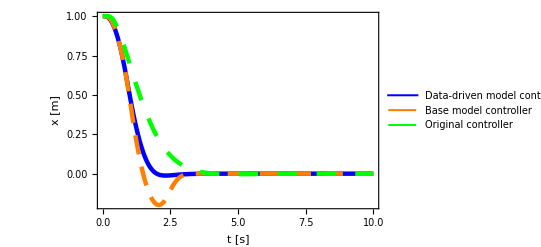
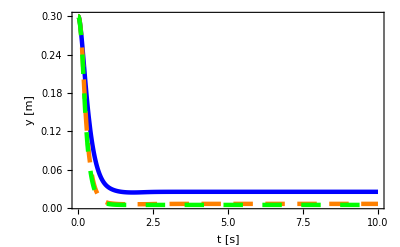
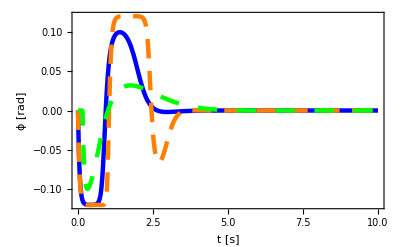
-Graphics- | -Graphics-
-Graphics- |

```mathematica
T=10;
paramsnew={1.42,0.51,6.13,4,29.7,1.47};
Eigenvalues[Jacobi@@Flatten[{paramsnew,liftnew}]]
sol1=Simulate[0,0,T,{1,0.3,0,0,0,0},ComputeEqsSaturation@@paramsnew];
sol2=Simulate[0,0,T,{1,0.3,0,0,0,0},ComputeEqsSaturation@@paramsorig];
sol3=Simulate[0,0,T,{1,0.3,0,0,0,0},ComputeEqsSaturation@@{K1,D1,K2,D2,K3,D3}];
plcomp=PlotxyϕCompare3[sol1,sol2,sol3,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_compcontr.png"}],plcomp];
```